```mathematica
ClearAll["Global`*"]
$HistoryLength=1;
SetOptions[EvaluationNotebook[],CellContext->Notebook]
$Context

packageDirectory:="C:\\Users\\User\\Documents\\Zvejnieks\\Bubble_Shape_Analysis\\Bubble Shape Analysis"
Import[packageDirectory<>"\\Shape Analyser.m"];

launchNukes[];

SetOptions[
Histogram,
{ImageSize->Large,ChartElementFunction->"GlassRectangle",ColorFunction->"GrayTones",LabelingFunction->Above,AspectRatio->Automatic}
];

SetOptions[
ListLinePlot,
{ImageSize->Large,AspectRatio->Automatic}
];

SetOptions[
ListPlot,
{ImageSize->Large,AspectRatio->Automatic}
];

SetOptions[
SmoothDensityHistogram,
{ImageSize->Large,AspectRatio->Automatic}
];
```

Notebook$$15$665863`

### Import Images

```mathematica
testImage=-Graphics-;
```

## Generalized Shape Analysis

### Get Phase Boundary Points & Bounds

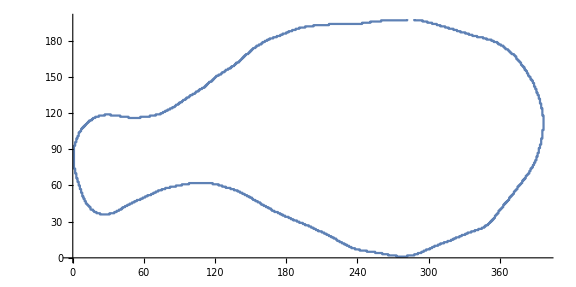

```mathematica
steppedBoundaryPoints=getPixelCoordinates@testImage;
bounds = getBoundingBox[testImage];
bubbleRegion=constructBubbleRegion[steppedBoundaryPoints];

steppedBoundaryPoints//ListLinePlot
```

### Iterative Polygon Simplification

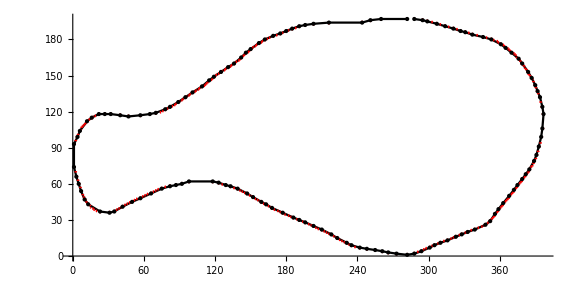

```mathematica
boundaryPoints=curveEvolution[steppedBoundaryPoints, 0.8, kc2];

ListLinePlot[boundaryPoints,PlotStyle->Black, Epilog->{{Red,PointSize@0.002,Point@steppedBoundaryPoints},{Black,PointSize@Large,Point@boundaryPoints}}]
```

### Interpolate & Uniformly Upsample the Boundary

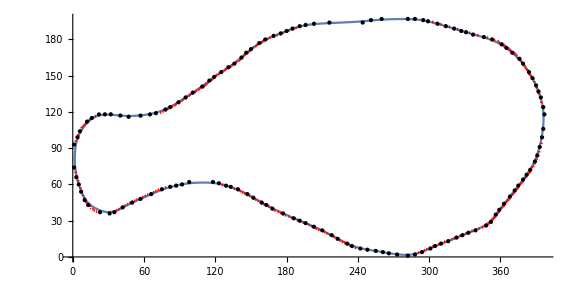

```mathematica
splineOrder = 10;
samplingPoints = 3000;

boundarySpline = buildBoundarySpline[boundaryPoints, splineOrder];
upsampledBoundary = uniformlySampleSpline[boundarySpline, samplingPoints];
ListLinePlot[upsampledBoundary, PlotStyle->PointSize@Tiny, Epilog->{{Red,PointSize@0.002,Point@steppedBoundaryPoints},{Black,PointSize@Large,Point@boundaryPoints}}]
```

### Compute the Boundary Curvature Profile & Local Extrema

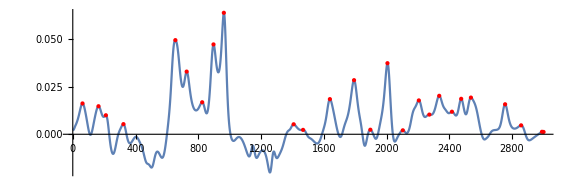

```mathematica
windowFactor=0.005;

curvatureProfile=getCurvatureProfile[upsampledBoundary, windowFactor];
curvatureExtrema = getCurvatureExtrema[curvatureProfile];

ListLinePlot[curvatureProfile, Epilog->{Red, PointSize@Large, Point@curvatureExtrema}, AspectRatio->1/3]
```

### Ramer–Douglas–Peucker downsampling

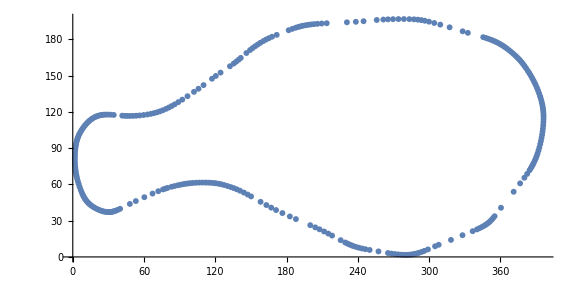

```mathematica
tolerance=0.02;
donwsampledBoundary=downsampleBoundary[upsampledBoundary,boundarySpline,tolerance,windowFactor];

donwsampledBoundary//ListPlot
```

### Generate the Voronoi Mesh & Get Interior Points

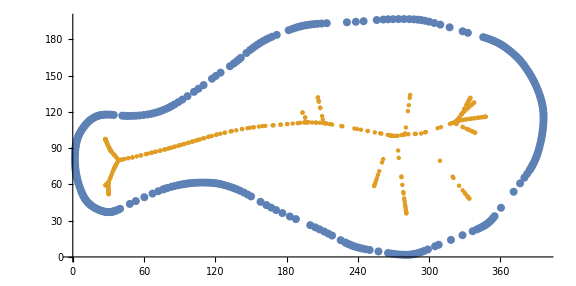

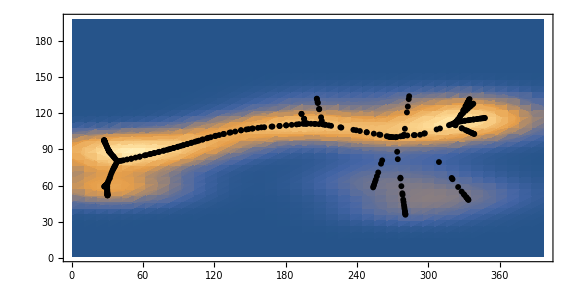

```mathematica
voronoiInternalPoints=getVoronoiInteriorNodes[donwsampledBoundary, bubbleRegion];
ListPlot[
{donwsampledBoundary,voronoiInternalPoints},
PlotStyle->{PointSize@0.01,Automatic}
]

Show@{
SmoothDensityHistogram[
voronoiInternalPoints,PlotRange->bounds,Mesh->5,MeshStyle->{Thick,Dashing[{0.02,0.02}],White}
],

ListPlot[voronoiInternalPoints,PlotStyle->Black]
}
```

### Generate the Assisting Skeleton

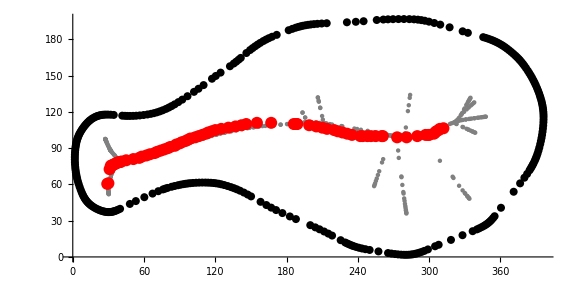

```mathematica
camberAssist=getAssistingSkeleton[testImage];

ListPlot[
{donwsampledBoundary,voronoiInternalPoints,camberAssist},
PlotStyle->{{Black,PointSize@0.01},Gray,{Red,PointSize@0.015}}
]
```

### Detect Voronoi Node Dendrites

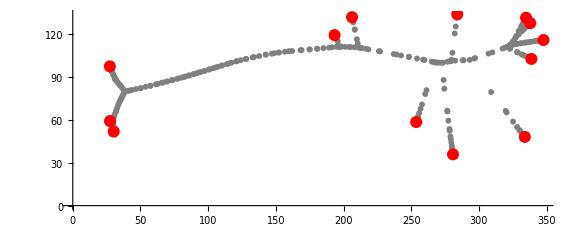

```mathematica
voronoiSpanningTree=getVoronoiSpanningTree[voronoiInternalPoints];
dendriteEndpoints=getVoronoiDendrites[voronoiSpanningTree];

ListPlot[
{voronoiInternalPoints,voronoiInternalPoints[[dendriteEndpoints]]},
PlotStyle->{Gray,{Red,PointSize@0.015}}
]
```

### Identify the Constructed Camber Line

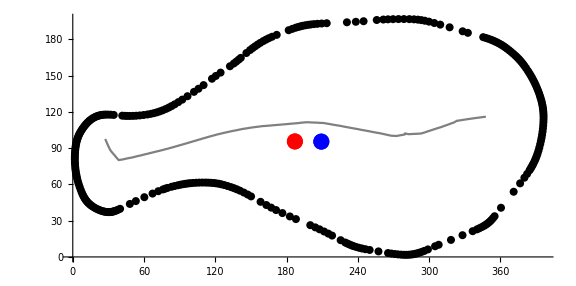

```mathematica
camberMain=constructCamberLine[voronoiInternalPoints,voronoiSpanningTree];
ListPlot[
{
donwsampledBoundary,camberMain,{Mean@donwsampledBoundary},{Mean@boundaryPoints}
},
PlotStyle->{
{Black,PointSize@0.01},
Gray,
{Red,PointSize@0.02},
{Blue,PointSize@0.02},
},
Joined->{False,True,False,False}
]
```

### Compute the Boundary Curvature Profile & Local Extrema

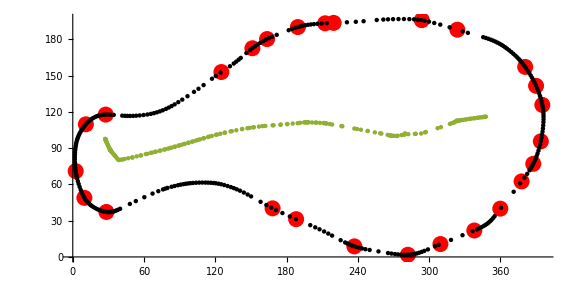

```mathematica
extremaLocations=mapExtremaToBoundary[boundarySpline,curvatureProfile];

ListPlot[
{extremaLocations,donwsampledBoundary,camberMain},
PlotStyle->{{Red,PointSize@0.02},Black,Automatic}
]
```

### Construct the Camber Line

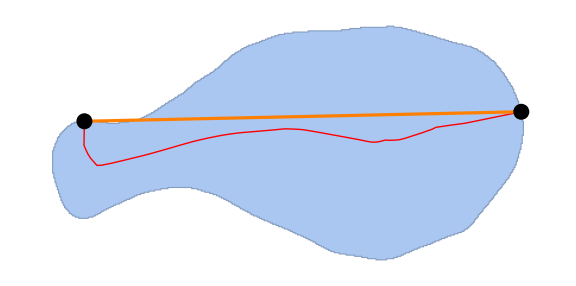

```mathematica
camberSplineOrder = 5;
camberSamplingPoints=100;

finalCamberLine=finishCamberLine[camberMain, extremaLocations];
chord=getChord[finalCamberLine];

downsampledCamberLine=resampleCamberLine[finalCamberLine, camberSplineOrder,camberSamplingPoints];

Show[
bubbleRegion,Epilog->{
{Red,Line@downsampledCamberLine},
{Orange,Thickness@0.004,Line@chord},
{Black,PointSize@0.02,Point@chord}
},
ImageSize->Large
]
```

### Compute Curvature VS Camber Line Arc Length

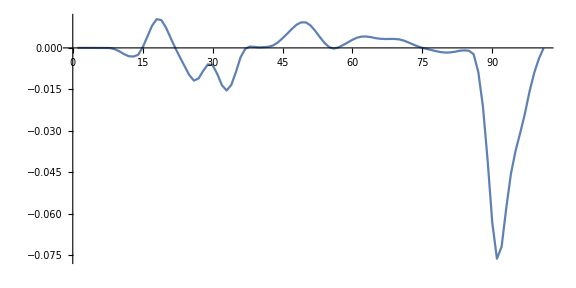

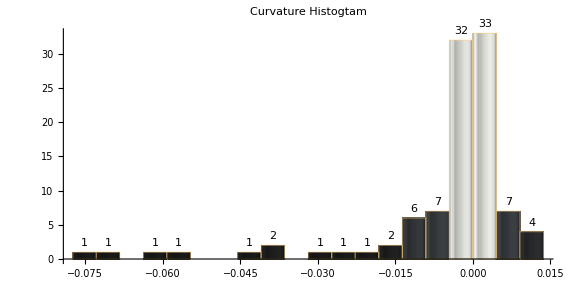

```mathematica
camberWindowFactor=0.05;
camberCurvatureProfile=getCurvatureProfile[downsampledCamberLine,camberWindowFactor];

ListLinePlot[
camberCurvatureProfile,
PlotRange->All,FrameLabel->{None,"κ"},Joined->{True,False},AspectRatio->1/2
]

Histogram[
camberCurvatureProfile,{"Raw",20},
PlotLabel->"Curvature Histogtam",FrameLabel->{"κ","N"},AspectRatio->1/2
]
```

### Compute Length, Coefficients & Tilt Angle and for the Principal Chord

```mathematica
chordParams=getChordParams[chord]
```

{lenght→367.596,tilt→1.2481}

### Compute Camber Line Length & Camber/Chord Length Ratio

```mathematica
camberLineParams=getCamberLineParams[downsampledCamberLine]
```

{lenght→405.17}

```mathematica
ratio=N@First@(({"lenght"}/.camberLineParams)/({"lenght"}/.chordParams))
```

1.10222